```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[x_, y_]]
```

```mathematica
SetDirectory["/Users/wenqiangfang/Dropbox (Personal)/WenqiangMaxHaneesh/ClausenPostbucklingandSensitivity/"]
```

/Users/wenqiangfang/Dropbox (Personal)/WenqiangMaxHaneesh/ClausenPostbucklingandSensitivity

```mathematica
Import["Sensitivity_constant_TEST.mat","Labels"]
```

{N,Nb,norm_r1,beta,rhat,d,Psi}

Constant p1

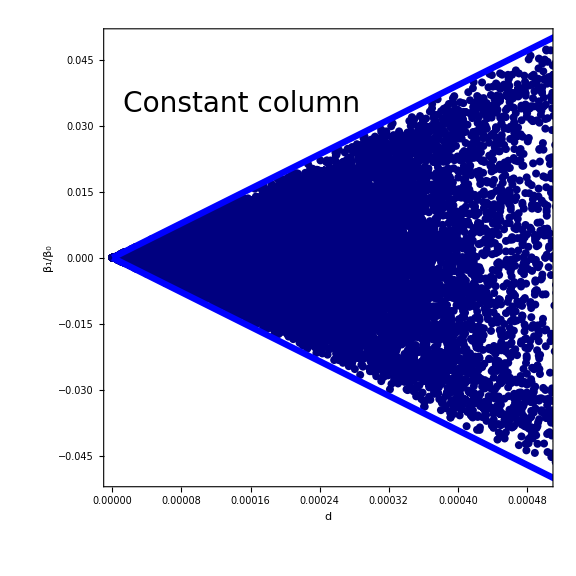

```mathematica
Block[{},
 data = Import["Sensitivity_constant_TEST.mat", {"Data", {6, 7}}];
d=Flatten@data[[1]];
β1β0 = Flatten@data[[2]];
data2=Partition[Riffle[d,β1β0],2];
p1=ListPlot[data2[[1;;300000;;10]],
PlotRange->{{0,0.0005},{-0.05,0.05}},
PlotStyle->Directive[RGBColor[0,0,0.5],PointSize[0.01]],
ImageSize->Large,
GridLines->None,
AspectRatio->1,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thickness[0.004],FontFamily->"Times",24],
FrameLabel->{Style["d",Black,FontFamily->"Times",24],Style["β_1/β_0",Black,FontFamily->"Times",24]},
RotateLabel->False,
ImageSize->500
];
pcons=Plot[{-97.97958971132712x,97.97958971132712x},{x,0,0007},PlotStyle->Directive[{RGBColor[0,0,1],Thickness[0.008]}]];
PConstant=Show[p1,pcons,Graphics[Text[Style["Constant column",Black,FontFamily->"Times",28],{0.00015,0.035}]]]
]
```

```mathematica
data//Dimensions
```

{2,1000000,1}

```mathematica
NotebookDirectory[]
```

/Users/wenqiangfang/Dropbox (Personal)/Clausen Postbuckling and Sensitivity/Figures/Figure_WF/

```mathematica
Export[NotebookDirectory[]<>"PConstant_v3.pdf",PConstant]
```

/Users/wenqiangfang/Dropbox (Personal)/Clausen Postbuckling and Sensitivity/Figures/Figure_WF/PConstant_v3.pdf

Clausen p2

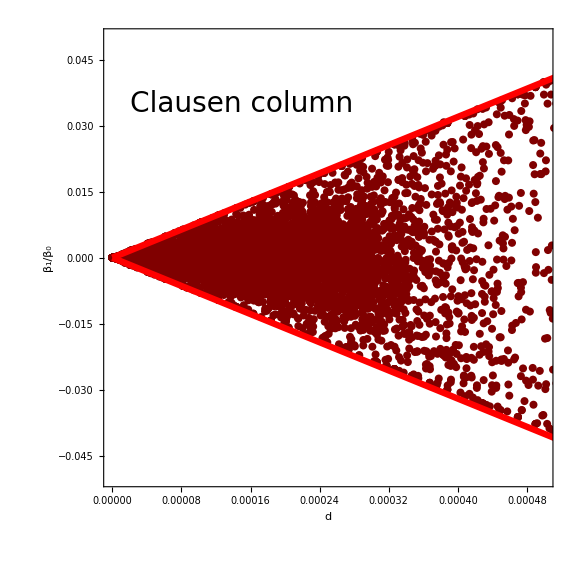

```mathematica
Block[{},
 data = Import["Sensitivity_clausen_TEST.mat", {"Data", {6, 7}}];
d=Flatten@data[[1]];
β1β0 = Flatten@data[[2]];
data2=Partition[Riffle[d,β1β0],2];
p2=ListPlot[data2[[1;;1000000;;50]],
PlotRange->{{0,0.0005},{-0.05,0.05}},
PlotStyle->Directive[RGBColor[0.5,0,0],PointSize[0.01]],
ImageSize->Large,
GridLines->None,
AspectRatio->1,
Axes->False,
Frame->True,
FrameStyle->Directive[Black,Thickness[0.004],FontFamily->"Times",24],
FrameLabel->{Style["d",Black,FontFamily->"Times",24],Style["β_1/β_0",Black,FontFamily->"Times",24]},
RotateLabel->False,
ImageSize->500];
pclau=Plot[{-80x,80x},{x,0,0005},PlotStyle->Directive[{RGBColor[1,0,0],Thickness[0.008]}]];
PClausen=Show[p2,pclau,Graphics[Text[Style["Clausen column",Black,FontFamily->"Times",28],{0.00015,0.035}]]]
]
```

```mathematica
data//Dimensions
```

{2,1000000,1}

```mathematica
Export[NotebookDirectory[]<>"PClausen_v3.pdf",PClausen]
```

/Users/wenqiangfang/Dropbox (Personal)/Clausen Postbuckling and Sensitivity/Figures/Figure_WF/PClausen_v3.pdf

Envelopes only

```mathematica
pclau=Plot[{-80x,80x},{x,0,0005},PlotStyle->Directive[{RGBColor[1,0,0],Thickness[0.008]}]];
```

```mathematica
pcons=Plot[{-97.97958971132712x,97.97958971132712x},{x,0,0007},PlotStyle->Directive[{RGBColor[0,0,1],Thickness[0.008]}]];
```

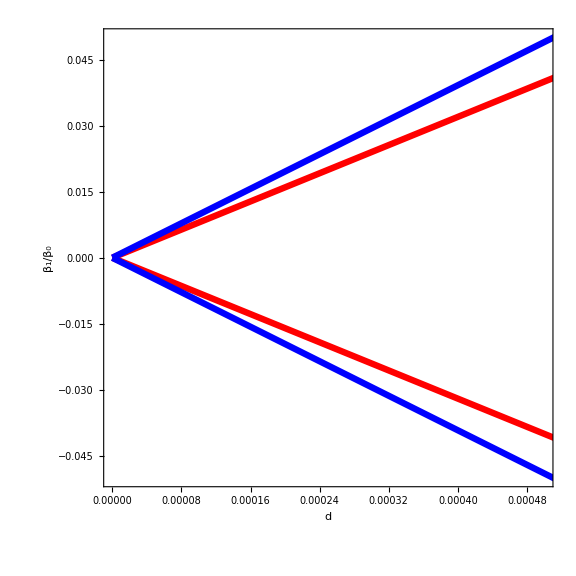

```mathematica
ppline=Show[pclau,pcons,PlotRange->{{0,0.0005},{-0.05,0.05}},
PlotStyle->Directive[RGBColor[0.5,0,0],PointSize[0.01]],
ImageSize->Large,
GridLines->None,
AspectRatio->1,
Axes->False,
AxesStyle->Directive[Black,FontFamily->"Times",24],
Frame->True,
FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["d",Black,FontFamily->"Times",24],Style["β_1/β_0",Black,FontFamily->"Times",24]},
RotateLabel->False]
```

Profile perturbation

### Constant

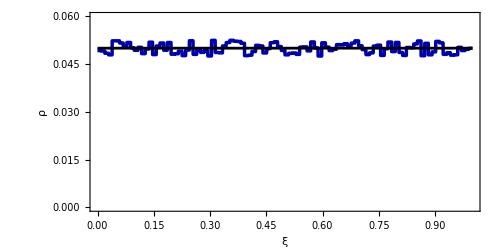

```mathematica
fre=100;
lim = 0.05 Subscript[r, c];
RRow=RandomReal[{-lim,lim},fre];
RR = Join[{RandomReal[{0.0,lim}]},RRow,{RandomReal[{0.0,lim}]}];
Len = Length@RR;
int = 1/Len;
step[x_]=Piecewise[{RR[[#]],int(#-1)<x<int#}&/@Range@Len];
Ppert2= Plot[Subscript[r, c]-step[x],{x,0,1},PlotStyle->{RGBColor[0,0,0.7],Thickness[0.005]}];
co1 = Plot[Subscript[r, c],{x,0,1},PlotStyle->{Black,Thickness[0.004]}];
PpertConstant=Show[Ppert2,co1
,PlotRange->{{0.0,1.0},{0,0.06}}
,Axes->False
,Frame->{{True,False},{True,False}}
,FrameStyle->Directive[Black,Thickness[0.004],FontFamily->"Times",24]
,FrameLabel->{Style["ξ",Black,FontFamily->"Times",24],Style["ρ",Black,FontFamily->"Times",24]}
,RotateLabel->False
,AspectRatio->1/2
,ImageSize->500]
```

### Clausen

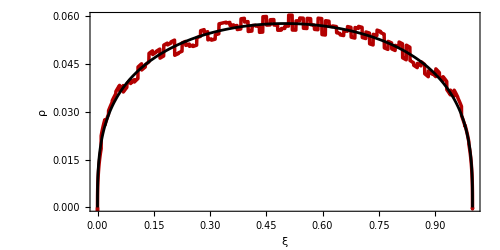

```mathematica
fre=100;
lim = 0.05 Subscript[r, a];
RRow=RandomReal[{-lim,lim},fre];
RR = Join[{RandomReal[{0.0,lim}]},RRow,{RandomReal[{0.0,lim}]}];
Len = Length@RR;
int = 1/Len;
step[x_]=Piecewise[{RR[[#]],int(#-1)<x<int#}&/@Range@Len];
Ppert1=ParametricPlot[{1/π(θ-1/2 Sin[2θ]),Subscript[r, a] Sin[θ]-step[1/π(θ-1/2 Sin[2θ])]},{θ,0,π},PlotStyle->{RGBColor[0.7,0,0],Thickness[0.005]}];
cl1=ParametricPlot[{1/π(θ-1/2 Sin[2θ]),Subscript[r, a] Sin[θ]},{θ,0,π},PlotStyle->{Black,Thickness[0.004]}];
PpertClausen=Show[Ppert1,cl1
,PlotRange->{{0.0,1.0},{0,0.06}}
,Axes->False
,Frame->{{True,False},{True,False}}
,FrameStyle->Directive[Black,Thickness[0.004],FontFamily->"Times",24]
,FrameLabel->{Style["ξ",Black,FontFamily->"Times",24],Style["ρ",Black,FontFamily->"Times",24]}
,RotateLabel->False
,AspectRatio->1/2
,ImageSize->500]
```

Assemble

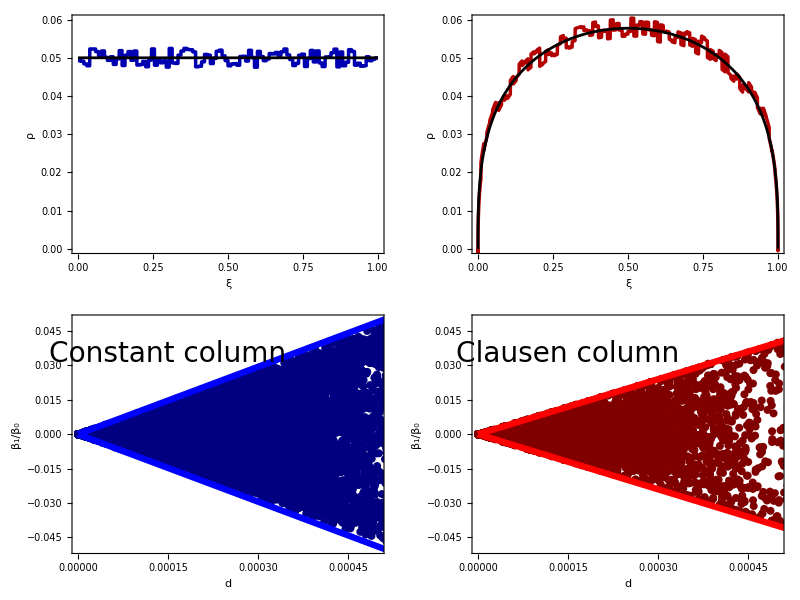

```mathematica
PltResult=Grid[{{PpertConstant,PpertClausen},{PConstant,PClausen}},Spacings->{1.4, 1.5}]
```

```mathematica
Export[NotebookDirectory[]<>"PltResult.pdf",PltResult]
```

/Users/wenqiangfang/Dropbox (Personal)/Clausen Postbuckling and Sensitivity/Figures/Figure_WF/PltResult.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/Users/wenqiangfang/Dropbox (Personal)/Clausen Postbuckling and Sensitivity/Figures/Figure_WF/PltResult.pdf"]]]
```

Isovolumetric vs scaling